Utilización promedio de los servidores: 50.3658%

Tasa media de llegadas: 0.0557118 clientes/minuto

Tasa media de servicios: 9.04271 minutos/cliente

Utilización promedio de los servidores: 49.5055%

Tasa media de llegadas: 0.0551364 clientes/minuto

Tasa media de servicios: 8.98291 minutos/cliente

Utilización promedio de los servidores: 49.6542%

Tasa media de llegadas: 0.0558917 clientes/minuto

Tasa media de servicios: 8.88504 minutos/cliente

Nro. promedio en el tiempo de clientes en sistema: 0.972596 clientes

Valor analítico - fórmula: 1. clientes

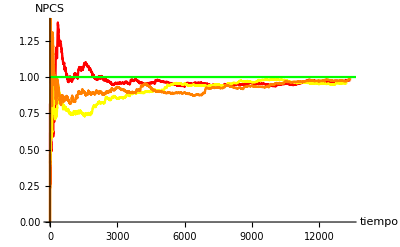

Nro. promedio en el tiempo de clientes en cola: 0.489086 clientes

Valor analítico - fórmula: 0.5 clientes

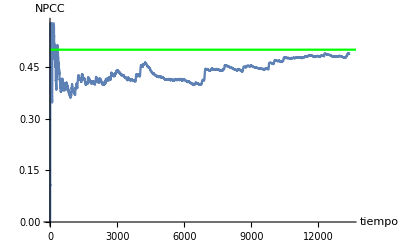

Demora promedio por cliente en cola: 8.75111 minutos

Valor analítico - fórmula: 9. minutos

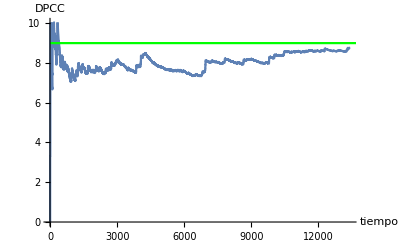

Tiempo promedio de clientes en sistema: 17.6361 minutos

Valor analítico - fórmula: 18. clientes

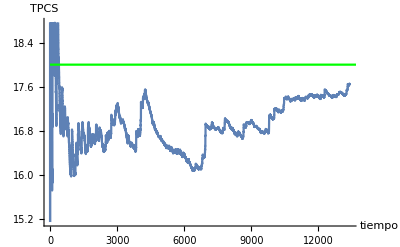

Nro. promedio en el tiempo de clientes en sistema: 0.985627 clientes

Valor analítico - fórmula: 1. clientes

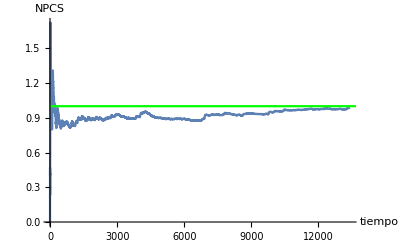

Area bajo la curva del subintervalo - 1: 3136.88 - Media del subintervalo: 0.794148

Area bajo la curva del subintervalo - 2: 3267.54 - Media del subintervalo: 0.827225

Area bajo la curva del subintervalo - 3: 4070.72 - Media del subintervalo: 1.03056

Area bajo la curva del subintervalo - 4: 3129.17 - Media del subintervalo: 0.792195

Area bajo la curva del subintervalo - 5: 3807.52 - Media del subintervalo: 0.963929

Area bajo la curva del subintervalo - 6: 3632.89 - Media del subintervalo: 0.91972

Area bajo la curva del subintervalo - 7: 4103.33 - Media del subintervalo: 1.03882

Area bajo la curva del subintervalo - 8: 2750.27 - Media del subintervalo: 0.696271

Area bajo la curva del subintervalo - 9: 4044.11 - Media del subintervalo: 1.02382

Area bajo la curva del subintervalo - 10: 4732.07 - Media del subintervalo: 1.19799

Area bajo la curva del subintervalo - 11: 2132.44 - Media del subintervalo: 0.539859

Area bajo la curva del subintervalo - 12: 3131.07 - Media del subintervalo: 0.792675

Area bajo la curva del subintervalo - 13: 3554.08 - Media del subintervalo: 0.899766

Area bajo la curva del subintervalo - 14: 3283.3 - Media del subintervalo: 0.831216

Area bajo la curva del subintervalo - 15: 2957.6 - Media del subintervalo: 0.748758

Area bajo la curva del subintervalo - 16: 6345.67 - Media del subintervalo: 1.6065

Area bajo la curva del subintervalo - 17: 3925.22 - Media del subintervalo: 0.993726

Area bajo la curva del subintervalo - 18: 4248.62 - Media del subintervalo: 1.0756

Area bajo la curva del subintervalo - 19: 3048.35 - Media del subintervalo: 0.771734

Area bajo la curva del subintervalo - 20: 4502.33 - Media del subintervalo: 1.13983

Area bajo la curva del subintervalo - 21: 3302.25 - Media del subintervalo: 0.836013

Area bajo la curva del subintervalo - 22: 5418.64 - Media del subintervalo: 1.37181

Area bajo la curva del subintervalo - 23: 4085.48 - Media del subintervalo: 1.0343

Area bajo la curva del subintervalo - 24: 4671.38 - Media del subintervalo: 1.18263

Area bajo la curva del subintervalo - 25: 4181.04 - Media del subintervalo: 1.05849

Area bajo la curva del subintervalo - 26: 4693.53 - Media del subintervalo: 1.18824

Area bajo la curva del subintervalo - 27: 3701.83 - Media del subintervalo: 0.937173

Area bajo la curva del subintervalo - 28: 3954.3 - Media del subintervalo: 1.00109

Area bajo la curva del subintervalo - 29: 3940.93 - Media del subintervalo: 0.997704

Area bajo la curva del subintervalo - 30: 4908.56 - Media del subintervalo: 1.24267

Media muestral: 0.984482

Grid[{1/2,1/3,1/3,3/10,17/30,10/21,4/7,17/18,29/18,141/55,125/33,137/26,1041/182,592/105,16/3,5,1457/306,803/171,461/95,997/210,699/154,1124/253,98/23,307/75,13365,211420096/89652745,26431319/11208267,52866971/22419882,422996681/179385842,211515673/89706315,750118/318155,211550609/89733106,423162137/179493006,211598402/89759901,52904002/22443325,105816671/44893350,47036401/19955578,211681139/89813503,35285267/14971151,30246991/12834330,423493097/179707430,211763884/89867121,105897175/44940264,105905843/44946968,7703351/3269358,211859489/89920755,15134079/6423869,4154793/1763678,4154793/1763678}]
 |  |  |  |

Valor analítico - fórmula: 2. clientes

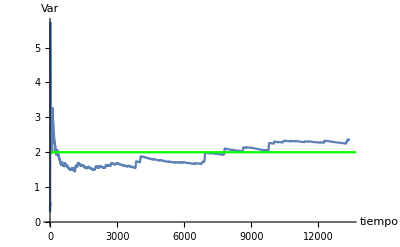

```mathematica
Quit;
ClearAll;
(***** DEFINICION DE FUNCIONES *****)
(* Rutina de tiempos *)
tiempos[] := Module[{menor, eme},
menor = Position[listaDeEventos, Min[listaDeEventos]];
eme = First[First[menor]];
tiempoUltimoEvento = reloj;
reloj = listaDeEventos[[eme]];
proximoEvento = tiposEventos[[eme]];
];

(* Rutina de arribos *)
arribos[] := Module[{tarr},
tarr = RandomVariate[ExponentialDistribution[1/tmEntreArribos]];
listaDeEventos[[1]]=reloj+tarr;
If[estadoServidor=="D",
estadoServidor="O";
tserv = RandomVariate[ExponentialDistribution[1/tmDeServicio]];
listaDeEventos = ReplacePart[listaDeEventos, 2->(reloj + tserv)];
tsAcumuladoUlt = tsAcumulado;(* 20170701 - Corrección del % de utilización del servidor *)
tsAcumulado = tsAcumulado + tserv;
completaronDemora = completaronDemora + 1;
,(* Else *)
areaQDeT = areaQDeT + (nroDeClientesEnCola * (reloj - tiempoUltimoEvento));
nroDeClientesEnCola = nroDeClientesEnCola + 1;
cola = Prepend[cola, reloj];
];
];

(* Rutina de partidas *)
partidas[] := Module[{tserv, tdem},
If[nroDeClientesEnCola > 0,
tserv = RandomVariate[ExponentialDistribution[1/tmDeServicio]];
listaDeEventos = ReplacePart[listaDeEventos, 2-> (reloj + tserv)];
tdem = reloj - cola[[1]];
demoraAcumulada = demoraAcumulada + tdem;
completaronDemora = completaronDemora + 1;
tsAcumuladoUlt = tsAcumulado;(* 20170701 - Corrección del % de utilización del servidor *)
tsAcumulado = tsAcumulado + tserv;
areaQDeT = areaQDeT + (nroDeClientesEnCola*(reloj-tiempoUltimoEvento));
nroDeClientesEnCola = nroDeClientesEnCola - 1;
cola = Delete[cola,1],(* Else *)
estadoServidor = "D"; 
listaDeEventos = ReplacePart[listaDeEventos, 2 -> 999999];
];
];

(* Cálculo de variables de respuesta *)
calculaVR[] := Module[{},
nroPromCliCola = areaQDeT/reloj;
nroPromCliSis = areaSDeT/reloj;(* 20170827 - Gráfico nro. promedio de clientes en el sistema *)
demPromPorCli = demoraAcumulada/completaronDemora;
demPromPorCliSis = (demoraAcumulada + tsAcumulado)/completaronDemora; (* 20170827 - Gráfico tiempo promedio de clientes en el sistema *)
(* utilizServ=tsAcumulado/reloj; 20170701 - Corrección del % de utilización del servidor *)
utilizServ=tsAcumuladoUlt/reloj;(* 20170701 - Corrección del % de utilización del servidor *)
];

nroPromCliSisTot =0.0;
For[k=1,k≤3,k++,

(* Definición e inicialización de variables *)
reloj = 0;
estadoServidor="D";
proximoEvento="null";
tiposEventos = {"Arribo","Partida"};
listaDeEventos = {};
cola={};
tsAcumulado = 0.0;
tsAcumuladoUlt = 0.0;(* 20170701 - Corrección del % de utilización del servidor *)
demoraAcumulada = 0.0;
nroDeClientesEnCola = 0;
areaQDeT = 0.0;
areaSDeT = 0.0;(* 20170827 - Gráfico nro. promedio de clientes en el sistema *)
nroCCUlt = 0;(* 20170827 - Gráfico nro. promedio de clientes en el sistema *)
tiempoUltimoEvento = 0.0;
completaronDemora = 0;
tmEntreArribos = 18.0;(* 1/λ *)
tmDeServicio = 9.0;(* 1/μ *)
tmax = 2000*60; (* 2000 horas - 120000 minutos *)
tasaLlegadas = 0.0; (* 20170618 *)
tasaServicios = 0.0; (* 20170618 *)
factorUtilizacion = 0.0; (* 20170618 *)
probClientes = 0.0; (* 20170618 *)
vRespuesta={};
areaSDeTNue = {}; (* 20170827 - Gráfico método de subintervalos *)
nroCS= 0; (* 20170905 - Gráfico 6 - Varianza n.ba clientes en sistema *)

listaDeEventos=Append[listaDeEventos,RandomVariate[ExponentialDistribution[1/tmEntreArribos]]];
listaDeEventos=Append[listaDeEventos,999999];
tabla=Table[{"Reloj", "Tipo_Ev", "t_Arribos","t_Partidas","estado_serv","nro_CC", "nro_CCD", "area_Qt", "ts_acum", "dem_Acum", "area_St", "nroCS"},1]; (* 20170827 - Gráfico nro. promedio de clientes en el sistema *)(* 20170905 - Gráfico 6 - Varianza n.ba clientes en sistema *)
tabla=Append[tabla, {reloj, proximoEvento, listaDeEventos[[1]],listaDeEventos[[2]],estadoServidor, nroDeClientesEnCola,completaronDemora, areaQDeT, tsAcumulado,demoraAcumulada,areaSDeT, nroCS}];(* 20170827 - Gráfico nro. promedio de clientes en el sistema *)(* 20170905 - Gráfico 6 - Varianza n.ba clientes en sistema *)
vRespuesta = Table[{"Reloj", "Nro_PTCC", "Dem_PPC", "Uti_PS", "Nro_PTCS", "Dem_PPCS", "NroCS"},1]; (* 20170827 - Gráficos nro. y tiempo promedio de clientes en el sistema *)
(* 20170905 - Gráfico 6 - Varianza n.ba clientes en sistema *)

(* Programa principal *)
While[reloj≤tmax,
a=tiempos[];
If[proximoEvento=="Arribo",
a=arribos[];
,
a=partidas[];
];

(* 20170827 - INICIO Gráfico nro. promedio de clientes en el sistema *)
(* If - 1 *)
If[(estadoServidor=="D"||nroDeClientesEnCola>0||nroCCUlt>0)&& reloj>0, 
(* If - 2 *)
If[nroDeClientesEnCola>0,
(* If - 3 *)
If[proximoEvento=="Partida",areaSDeT = areaSDeT + ((reloj-tiempoUltimoEvento)*(nroCCUlt+1)),(* Else - 3 *)
areaSDeT = areaSDeT + ((reloj-tiempoUltimoEvento)*nroDeClientesEnCola)];nroCCUlt = nroDeClientesEnCola,(* Else - 2 *)
areaSDeT = areaSDeT + ((reloj-tiempoUltimoEvento)*(nroCCUlt+1));nroCCUlt = 0;],(* Else - 1 *)
nroCCUlt = 0
];
(* 20170827 - FIN Gráfico nro. promedio de clientes en el sistema *)

If[estadoServidor=="O",If[nroDeClientesEnCola==0,nroCS=1,nroCS=nroCCUlt+1],nroCS = 0];(* 20170905 - Gráfico 6 - Varianza n.ba clientes en sistema *)

tabla=Append[tabla,{reloj,proximoEvento,listaDeEventos[[1]],listaDeEventos[[2]],estadoServidor,nroDeClientesEnCola,completaronDemora,areaQDeT,tsAcumulado,demoraAcumulada, areaSDeT,nroCS}]; (* 20170827 - Gráfico nro. promedio de clientes en el sistema *)(* 20170905 - Gráfico 6 - Varianza n.ba clientes en sistema *)
a=calculaVR[];
vRespuesta=Append[vRespuesta,{reloj,nroPromCliCola,demPromPorCli,utilizServ,nroPromCliSis,demPromPorCliSis, nroCS}];(* 20170827 - Gráficos nro. y tiempo promedio de clientes en el sistema *)(* 20170905 - Gráfico 6 - Varianza n.ba clientes en sistema *)
];

nroPromCliCola=areaQDeT/reloj;
nroPromCliSis=areaSDeT/reloj; (* 20170827 - Gráfico nro. promedio de clientes en el sistema *)
demPromPorCli=demoraAcumulada/completaronDemora;
demPromPorCliSis = (demoraAcumulada+tsAcumulado)/completaronDemora; (* 20170827 - Gráfico tiempo promedio de clientes en el sistema *)
(*utilizServ=tsAcumulado/reloj; 20170701 - Corrección del % de utilización del servidor *)
utilizServ=tsAcumuladoUlt/reloj;(* 20170701 - Corrección del % de utilización del servidor *)
tasaLlegadas =completaronDemora/tiempoUltimoEvento; (* 20170618 *)
tasaServicios = tsAcumulado/completaronDemora; (* 20170618 *)
factorUtilizacion = tmEntreArribos^(-1)/tmDeServicio^(-1); (* λ/μ - 20170618 *)
probClientes =(1-factorUtilizacion)*(factorUtilizacion)^3; (* (1-(λ/μ)).(λ/μ)3 - 20170618 *)

(* Reporte *)
Print["Utilización promedio de los servidores: ",utilizServ*100,"%"]
Print["Tasa media de llegadas: ",tasaLlegadas," clientes/minuto"] (* 20170618 *)
Print["Tasa media de servicios: ",tasaServicios," minutos/cliente\n"] (* 20170618 *)
(* Print["Probabilidad de exactamente 3 elementos en el sistema: ",probClientes*100,"%"] *)

Grid[tabla];
Grid[vRespuesta];

(* 20170827 - Gráfico 7 - Nro. promedio en el tiempo de clientes en sistema *)
(* Creamos una tabla sólo con el nro. promedio de clientes en sistema *)
nroPCSt = vRespuesta[[All,5]];
nroPCSt = Delete[nroPCSt,1];
Grid[nroPCSt];
If[k==1,g10 = ListLinePlot[nroPCSt, AxesLabel->{tiempo,NPCS},PlotRange->All,PlotStyle->Red];,If[k==2,g20 = ListLinePlot[nroPCSt, AxesLabel->{tiempo,NPCS},PlotRange->All,PlotStyle->Yellow];,g30 = ListLinePlot[nroPCSt, AxesLabel->{tiempo,NPCS},PlotRange->All,PlotStyle->Orange];]];
nroPCSm = factorUtilizacion*((1-factorUtilizacion)^(-1)); (* valor analítico - fórmula *)
solana4 = Plot[nroPCSm,{x,0,tiempoUltimoEvento},PlotStyle->Green];
nroPromCliSisTot = nroPromCliSisTot + nroPromCliSis;

 (* Print["\nNro. promedio en el tiempo de clientes en sistema: ",nroPromCliSis," clientes"]; *)
 (* Print["Valor analítico - fórmula: ",nroPCSm," clientes"]; *)

];(* Fin For *)
Print["\nNro. promedio en el tiempo de clientes en sistema: ",nroPromCliSisTot/3," clientes"]; 
 Print["Valor analítico - fórmula: ",nroPCSm," clientes"]; 
Show[g10,g20,g30,solana4]

Grid[tabla];(* 20170905 - Gráfico 6 - Varianza n.ba clientes en sistema *)


(* Gráficos *)
(* Gráfico 1 - Nro. promedio en el tiempo de clientes en cola *)
(* Creamos una tabla sólo con el nro. promedio de clientes en cola *)
nroPCCt = vRespuesta[[All,2]];
nroPCCt = Delete[nroPCCt,1];
Grid[nroPCCt];
g1 = ListLinePlot[nroPCCt, AxesLabel->{tiempo,NPCC}];
nroPCCm = (factorUtilizacion)^2*(1-factorUtilizacion)^(-1); (* valor analítico - fórmula *)
solana1 = Plot[nroPCCm,{x,0,tiempoUltimoEvento},PlotStyle->Green];
Print["Nro. promedio en el tiempo de clientes en cola: ",nroPromCliCola," clientes"];
Print["Valor analítico - fórmula: ",nroPCCm," clientes"];
Show[g1,solana1]

(* Gráfico 2 - Demora promedio por cliente en cola *)
(* Creamos una tabla sólo con la demora promedio de clientes en cola *)
demPCCt = vRespuesta[[All,3]];
demPCCt = Delete[demPCCt,1];
Grid[demPCCt];
g2 = ListLinePlot[demPCCt, AxesLabel->{tiempo,DPCC}];
demPCCm = (tmEntreArribos^(-1)/tmDeServicio^(-2))*(1-factorUtilizacion)^(-1); (* valor analítico - fórmula *)
solana2 = Plot[demPCCm,{x,0,tiempoUltimoEvento},PlotStyle->Green];
Print["\nDemora promedio por cliente en cola: ",demPromPorCli, " minutos"];
Print["Valor analítico - fórmula: ",demPCCm," minutos"];
Show[g2,solana2]

(* 20170827 - Gráfico 3 - Tiempo promedio de clientes en sistema *)
(* Creamos una tabla sólo con el tiempo promedio de clientes en sistema *)
tiePCSt = vRespuesta[[All,6]];
tiePCSt = Delete[tiePCSt,1];
Grid[tiePCSt];
g3 = ListLinePlot[tiePCSt, AxesLabel->{tiempo,TPCS}];
tiePCSm = tmDeServicio*(1-factorUtilizacion)^(-1); (* valor analítico - fórmula *)
solana3 = Plot[tiePCSm,{x,0,tiempoUltimoEvento},PlotStyle->Green];
Print["\nTiempo promedio de clientes en sistema: ",demPromPorCliSis," minutos"];
Print["Valor analítico - fórmula: ",tiePCSm," clientes"];
Show[g3,solana3]

(* 20170827 - Gráfico 4 - Nro. promedio en el tiempo de clientes en sistema *)
(* Creamos una tabla sólo con el nro. promedio de clientes en sistema *)
nroPCSt = vRespuesta[[All,5]];
nroPCSt = Delete[nroPCSt,1];
Grid[nroPCSt];
g4 = ListLinePlot[nroPCSt, AxesLabel->{tiempo,NPCS},PlotRange->All];
nroPCSm = factorUtilizacion*((1-factorUtilizacion)^(-1)); (* valor analítico - fórmula *)
solana4 = Plot[nroPCSm,{x,0,tiempoUltimoEvento},PlotStyle->Green];
Print["\nNro. promedio en el tiempo de clientes en sistema: ",nroPromCliSis," clientes"];
Print["Valor analítico - fórmula: ",nroPCSm," clientes"];
Show[g4,solana4]

(* 20170827 - Gráfico 5 - Método de subintervalos *)
lonPerTra = 1500; (* Longitud en minutos del período transitorio *)
(* lonPerTra = 80;  Prueba *)
lonSubInt = 3950; (* Longitud en minutos de cada subintervalo *)
(* lonSubInt = 25;  Prueba *)
canSubInt = Round[(tmax-lonPerTra)/lonSubInt];(* cantidad de subintervalos *)
subInt = tabla[[All,{1,11}]];
subInt = Delete[subInt,1];
solana5 = ParametricPlot[{{lonPerTra,t},{lonPerTra+lonSubInt,t},{lonPerTra+2*lonSubInt,t},{lonPerTra+3*lonSubInt,t},{lonPerTra+4*lonSubInt,t},{lonPerTra+5*lonSubInt,t},{lonPerTra+6*lonSubInt,t},{lonPerTra+7*lonSubInt,t},{lonPerTra+8*lonSubInt,t},{lonPerTra+9*lonSubInt,t},{lonPerTra+10*lonSubInt,t}},{t,0,tiempoUltimoEvento},PlotStyle->Green];
Grid[subInt];
medMue = 0.0;
tieLim = lonPerTra+lonSubInt;
(* PPrint["1 - tieLim: ", tieLim]; *)
i=1;
While [subInt[[i,1]]<lonPerTra,areaSDeTAnt= subInt[[i,2]];i++] (* quitamos el período inicial *)
(* Print["1 - areaSDeTAnt: ", areaSDeTAnt]; *)

For[j=1,j<=canSubInt,j++,
tieLim = lonPerTra+(j*lonSubInt);
While[subInt[[i,1]]<tieLim,areaSDeTNue = Append[areaSDeTNue,subInt[[i,2]]];i++] ;
medMue = medMue + ((Last[areaSDeTNue]-areaSDeTAnt)/lonSubInt)/canSubInt;
Print["Area bajo la curva del subintervalo - ",j, ": ", Last[areaSDeTNue]-areaSDeTAnt, " - Media del subintervalo: ",(Last[areaSDeTNue]-areaSDeTAnt)/lonSubInt]; (* tabla de áreas de cada subintervalo *)
areaSDeTAnt = Last[areaSDeTNue];
(* Print[j, " - areaSDeTAnt: ", areaSDeTAnt]; *)
]
Print["Media muestral: ",medMue];
Show[g4,solana5];

(* 20170905 - Gráfico 6 - Varianza n.ba clientes en sistema *)
varCS={};
varCSAux={};
(* Creamos una tabla sólo con el nro. de clientes en sistema *)
nroCSt = vRespuesta[[All,7]];
nroCSt = Delete[nroCSt,1];
Grid[nroCSt];
For[k=1,k≤Length[nroCSt]+1,k++,If[k≤Length[nroCSt],varCS = Append[varCS,nroCSt[[k]]]];If[Length[varCS]>1,varCSAux=Append[varCSAux,Variance[varCS]]]];
Grid[varCSAux]
g5 = ListLinePlot[varCSAux, AxesLabel->{tiempo,Var},PlotRange->All];
nroCSm = factorUtilizacion/(1-factorUtilizacion)^2; (* valor analítico - fórmula *)
solana6 = Plot[nroCSm,{x,0,tiempoUltimoEvento},PlotStyle->Green];
Print["Valor analítico - fórmula: ",nroCSm," clientes"];
Show[g5,solana6]
```

```mathematica
(□_□)_□
```

(□_□)_□